```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/robel/projects/GraphP/wackycrazyidea/partition/baseline

```mathematica
data = Import["distribution_plot.dat", "Data"]
```

{{2,4008},{3,1601},{4,767},{5,458},{6,278},{135,1},{8,136},{9,109},{10,69},{11,62},{12,43},{13,31},{142,1},{15,19},{16,17},{17,19},{18,15},{19,14},{20,11},{21,7},{22,9},{23,10},{24,3},{25,6},{27,3},{28,6},{29,5},{30,2},{31,3},{32,1},{33,3},{34,2},{35,2},{36,3},{37,1},{39,2},{40,1},{41,3},{42,1},{7,203},{44,1},{45,3},{46,2},{47,1},{48,1},{49,1},{178,1},{51,1},{54,1},{58,1},{59,1},{160,1},{67,1},{69,2},{70,1},{74,1},{80,1},{82,1},{14,37},{93,1},{94,1},{50,2},{121,1}}

```mathematica
model[a_,b_,c_,x_]:= Exp[a]*x^b+ c
```

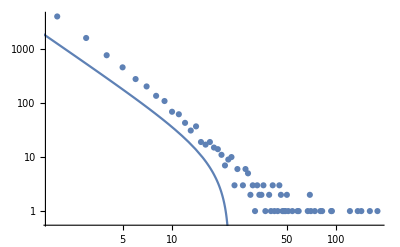

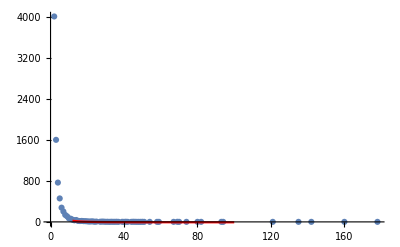

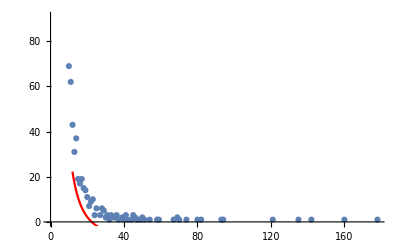

```mathematica
Show[
ListLogLogPlot[data, PlotRange->All],
LogLogPlot[model[8.59,-2.0859,-8.2,x],{x,1,100}]
]
Show[
ListPlot[data, PlotRange->All],
Plot[model[8.59,-2.0859,-8.219,x],{x,1,100}, PlotStyle->Red]
]
Show[
ListPlot[data],
Plot[model[8.59,-2.0859,-8.219,x],{x,1,100}, PlotStyle->Red]
]
```

```mathematica
FindFit[data,model[a,b,c,x],{a,b,c},x, MaxIterations->10000]
```

{a→9.92835,b→-2.34895,c→-4.35397}

```mathematica
model[a,b,c,x]
```

c+ⅇ^a x^b

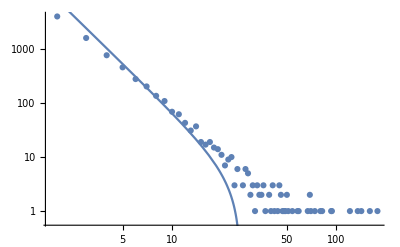

```mathematica
Show[
ListLogLogPlot[data, PlotRange->All],
LogLogPlot[model[11.06,-2.97,-3.94,x],{x,1,100}]
]
```